```mathematica
;
```

Last updated:   Thu 13 Jan 2022

## See

```mathematica
Labeled[[Entity["City",{"Lagos","Lagos","Nigeria"}],#,ImageSize->300],#]&@DateObject[{2020,6,5,12},"Hour","Gregorian",0.]
```

-Graphics-SENWHour beginning: Fri 5 Jun 2020 12 pmGMT

## Hear

```mathematica
(* mean air temperature and pressure at midday *)
{airT,airP}=Through[{AirTemperatureData,AirPressureData}[Entity["City",{"Lagos","Lagos","Nigeria"}],DateObject[{2020,6,5,12},"Hour","Gregorian",0.],Mean,UnitSystem->"Metric"]]
```

{33.3 °C,1014.8 mbar}

```mathematica
(* mean dew point temperature at midday *)
dew=Mean@WeatherData[Entity["City",{"Lagos","Lagos","Nigeria"}],"DewPoint",DateObject[{2020,6,5,12},"Hour","Gregorian",0.]]
```

25.6 °C

```mathematica
(* sound of a crowd *)
audio=Audio@AudioData@ExampleData[{"Audio","Crowd"}]
```

```mathematica
(* attenuated sound *)
attAudio=With[{audio=audio},
AirSoundAttenuation[<|"DryBulbTemperature"->airT,"Pressure"->airP,"DewPointTemperature"->dew|>,audio,Quantity[10, "Meters"],Method->"IncludeDispersion"]]
```

### See what you heard

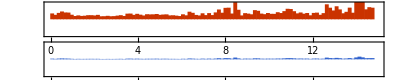

```mathematica
AudioPlot[{audio,attAudio},]
```